```mathematica
Pristine ZrC electron transport;
```

#### Some basic information;

```mathematica
alatts={4.575,4.600,4.625,4.6583,4.685,4.730,4.759,4.801,4.850};
tempps={0,10,300,500,760,1000,1500,1900,2500,3200,3800};
temppps=tempps[[2;;11]];
temps2={300,300,760,1900,2500,3200,3800};
temps3={300,760,1900,2500,3200,3800};
THz2meV=1/4.135665538536;K2meV=0.086173324;kjmol2evatom=1/(96.487*64);
Nat=64;Natvac=63;mass={91.224,12.0107,1};
ang2bohr=1/0.529177208;ev2har=1/27.211396;kB=1000*8.617332478*10^−5;
eVperAng2harperbohr=ev2har/ang2bohr;eVperAng22harperbohr2=ev2har/ang2bohr/ang2bohr;
HarBohr=meVperAng22harperbohr2=0.001*ev2har/ang2bohr/ang2bohr;
(*Constant, Fermi-Dirac and Fermi-Dirac changing with energy*)
K2eV=8.617332478*10^−5;
fermiDirac[energy_,temp_]:=1/(Exp[energy/(K2eV*temp)]+1)
(*define sigma and8 kappa kernels*)
(*temp in energy units*)
sigmaK[energy_,temp_]:=-D[fermiDirac[energy,temp],energy]
kappaK[energy_,temp_]:=-(1/temp)*(energy^2)*D[fermiDirac[energy,temp],energy]
eV2ryd=1/13.605698066;ryd2eV=13.605698066;
```

#### Import data;

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/NEB/FINAL_PATHS_FOR_PAPER/"];
file={"3_vol_temp_dist_energy"};
NEBdata=Table[ReadList[file[[i]],{Number, Number,Number, Number,Number, Number,Number, Number,Number, Number,Number, Number,Number}],{i,1,1}][[1]];
```

```mathematica
Transpose[NEBdata]
```

{{0,1,2,3,4},{4.6583,4.6583,4.6583,4.6583,4.6583},{0,0,0,0,0},{0.,0.540279,0.881051,1.93139,4.34964},{0.,0.459286,0.390465,0.995135,-3.36282},{4.759,4.759,4.759,4.759,4.759},{2479,2479,2479,2479,2479},{0.,0.505926,0.917487,2.29007,3.5768},{0.,0.415663,0.297066,1.18229,-2.82737},{4.85,4.85,4.85,4.85,4.85},{3821,3821,3821,3821,3821},{0.,0.491838,0.973187,2.42791,3.66887},{0.,0.408561,0.224986,1.4023,-2.07754}}

```mathematica
index=Transpose[NEBdata][[{1}]][[1]]
vols=Transpose[NEBdata][[{2,6,10}]]
temp=Transpose[NEBdata][[{3,7,11}]]
dist=Transpose[NEBdata][[{4,8,12}]]
e0s=Transpose[NEBdata][[{5,9,13}]]
```

{0,1,2,3,4}

{{4.6583,4.6583,4.6583,4.6583,4.6583},{4.759,4.759,4.759,4.759,4.759},{4.85,4.85,4.85,4.85,4.85}}

{{0,0,0,0,0},{2479,2479,2479,2479,2479},{3821,3821,3821,3821,3821}}

{{0.,0.540279,0.881051,1.93139,4.34964},{0.,0.505926,0.917487,2.29007,3.5768},{0.,0.491838,0.973187,2.42791,3.66887}}

{{0.,0.459286,0.390465,0.995135,-3.36282},{0.,0.415663,0.297066,1.18229,-2.82737},{0.,0.408561,0.224986,1.4023,-2.07754}}

```mathematica
dist[[1]][[-1]]
```

4.34964

```mathematica
Flatten[{dist[[1]],2dist[[1]][[-1]]-dist[[1]][[-2]]}]
```

{0.,0.540279,0.881051,1.93139,4.34964,6.76788}

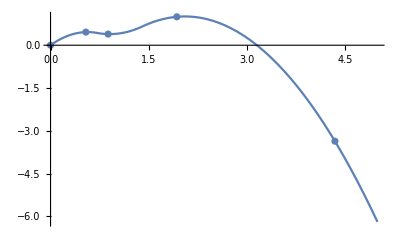

```mathematica
diste0s=Table[Transpose@{dist[[i]],e0s[[i]]},{i,1,3}];
ListLinePlot@diste0s;
Show[{Plot[Interpolation[diste0s[[1]],Method->"Spline",InterpolationOrder->2][x],{x,0,5}],ListPlot@diste0s[[1]]}];
```

```mathematica
(*Function to force the gradients to be correct either side*)
delta=5;
F[{a_,b_}]:={{a,b},{a+delta/1000,b},{a-delta/1000,b}}
diste0sGrad=Table[Partition[Flatten@Table[F[diste0s[[i]][[j]]],{j,1,Length[diste0s[[i]]]}],2],{i,1,3}]
diste0sGradGP=Table[Flatten[{#1->#2}&@@@diste0sGrad[[i]]],{i,1,3}]
Pdiste0sGradGP=Table[Predict[diste0sGradGP[[i]],Method->"GaussianProcess"],{i,1,3}]
```

{{{0.,0.},{0.005,0.},{-0.005,0.},{0.540279,0.459286},{0.545279,0.459286},{0.535279,0.459286},{0.881051,0.390465},{0.886051,0.390465},{0.876051,0.390465},{1.93139,0.995135},{1.93639,0.995135},{1.92639,0.995135},{4.34964,-3.36282},{4.35464,-3.36282},{4.34464,-3.36282}},{{0.,0.},{0.005,0.},{-0.005,0.},{0.505926,0.415663},{0.510926,0.415663},{0.500926,0.415663},{0.917487,0.297066},{0.922487,0.297066},{0.912487,0.297066},{2.29007,1.18229},{2.29507,1.18229},{2.28507,1.18229},{3.5768,-2.82737},{3.5818,-2.82737},{3.5718,-2.82737}},{{0.,0.},{0.005,0.},{-0.005,0.},{0.491838,0.408561},{0.496838,0.408561},{0.486838,0.408561},{0.973187,0.224986},{0.978187,0.224986},{0.968187,0.224986},{2.42791,1.4023},{2.43291,1.4023},{2.42291,1.4023},{3.66887,-2.07754},{3.67387,-2.07754},{3.66387,-2.07754}}}

{{0.→0.,0.005→0.,-0.005→0.,0.540279→0.459286,0.545279→0.459286,0.535279→0.459286,0.881051→0.390465,0.886051→0.390465,0.876051→0.390465,1.93139→0.995135,1.93639→0.995135,1.92639→0.995135,4.34964→-3.36282,4.35464→-3.36282,4.34464→-3.36282},{0.→0.,0.005→0.,-0.005→0.,0.505926→0.415663,0.510926→0.415663,0.500926→0.415663,0.917487→0.297066,0.922487→0.297066,0.912487→0.297066,2.29007→1.18229,2.29507→1.18229,2.28507→1.18229,3.5768→-2.82737,3.5818→-2.82737,3.5718→-2.82737},{0.→0.,0.005→0.,-0.005→0.,0.491838→0.408561,0.496838→0.408561,0.486838→0.408561,0.973187→0.224986,0.978187→0.224986,0.968187→0.224986,2.42791→1.4023,2.43291→1.4023,2.42291→1.4023,3.66887→-2.07754,3.67387→-2.07754,3.66387→-2.07754}}

{PredictorFunction[…],PredictorFunction[…],PredictorFunction[…]}

```mathematica
legends={{"T=0 K turning-point data"},{"T=2500 K turning-point data"},{"T=3800 K turning-point data"}};
```

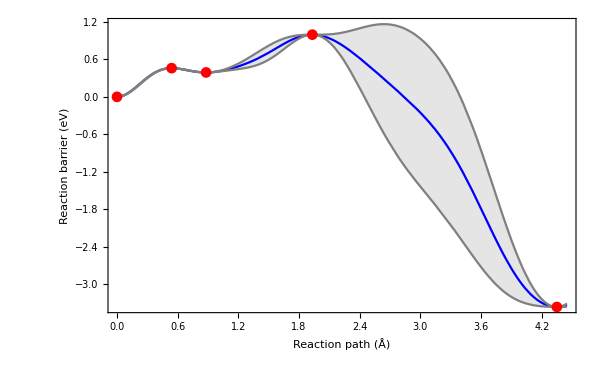

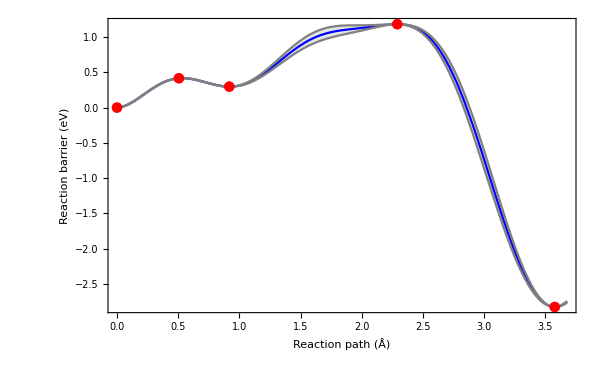

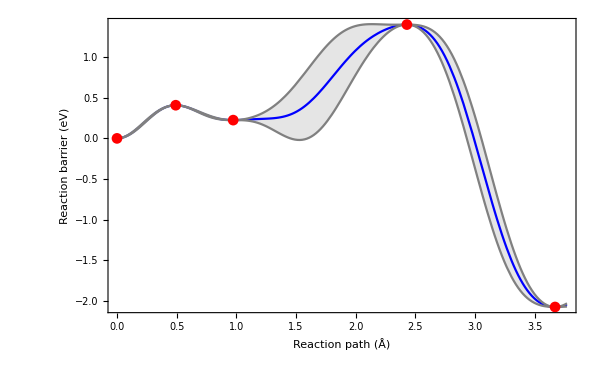

```mathematica
With[{vol=1},Show[Plot[{Pdiste0sGradGP[[vol]][x],Pdiste0sGradGP[[vol]][x]+StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]],Pdiste0sGradGP[[vol]][x]-StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]]},{x,0,Evaluate[dist[[vol]][[-1]]+0.1]},PlotStyle->{Blue,Gray,Gray},Filling->{2->{3}},Exclusions->"None",PerformanceGoal->"Speed",PlotLegends->Placed[{"Prediction","1-σ confidence interval"},{0.2,0.2}],Frame->True,FrameLabel->{"Reaction path (Å)","Reaction barrier (eV)"},ImageSize->600],ListPlot[List@@@diste0s[[vol]],PlotStyle->Red,PlotLegends->Placed[legends[[vol]],{0.2,0.2}]]]]
With[{vol=2},Show[Plot[{Pdiste0sGradGP[[vol]][x],Pdiste0sGradGP[[vol]][x]+StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]],Pdiste0sGradGP[[vol]][x]-StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]]},{x,0,Evaluate[dist[[vol]][[-1]]+0.1]},PlotStyle->{Blue,Gray,Gray},Filling->{2->{3}},Exclusions->"None",PerformanceGoal->"Speed",PlotLegends->Placed[{"Prediction","1-σ confidence interval"},{0.2,0.2}],Frame->True,FrameLabel->{"Reaction path (Å)","Reaction barrier (eV)"},ImageSize->600],ListPlot[diste0s[[vol]],PlotStyle->Red,PlotLegends->Placed[legends[[vol]],{0.2,0.2}]]]]
With[{vol=3},Show[Plot[{Pdiste0sGradGP[[vol]][x],Pdiste0sGradGP[[vol]][x]+StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]],Pdiste0sGradGP[[vol]][x]-StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]]},{x,0,Evaluate[dist[[vol]][[-1]]+0.1]},PlotStyle->{Blue,Gray,Gray},Filling->{2->{3}},Exclusions->"None",PerformanceGoal->"Speed",PlotLegends->Placed[{"Prediction","1-σ confidence interval"},{0.2,0.2}],Frame->True,FrameLabel->{"Reaction path (Å)","Reaction barrier (eV)"},ImageSize->600],ListPlot[diste0s[[vol]],PlotStyle->Red,PlotLegends->Placed[legends[[vol]],{0.2,0.2}]]]]
```

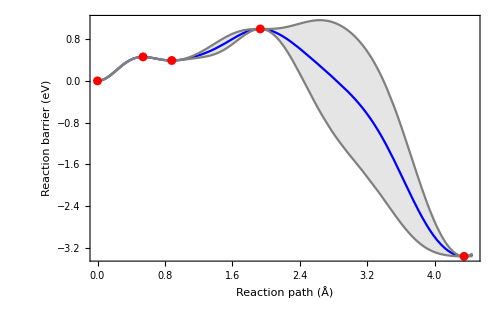

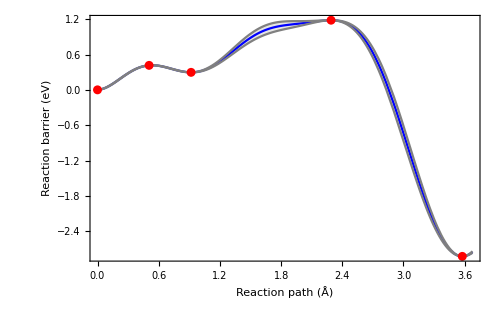

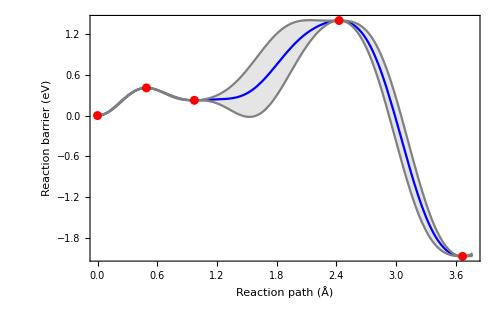

```mathematica
gp1=With[{vol=1},Show[Plot[{Pdiste0sGradGP[[vol]][x],Pdiste0sGradGP[[vol]][x]+StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]],Pdiste0sGradGP[[vol]][x]-StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]]},{x,0,Evaluate[dist[[vol]][[-1]]+0.1]},PlotStyle->{Blue,Gray,Gray},Filling->{2->{3}},Exclusions->"None",PerformanceGoal->"Speed",PlotLegends->Placed[{"Prediction","1-σ confidence interval"},{0.2,0.2}],Frame->True,FrameLabel->{Style["Reaction path (Å)",FontSize->12],Style["Reaction barrier (eV)",FontSize->12]},ImageSize->500],ListPlot[List@@@diste0s[[vol]],PlotStyle->Red,PlotLegends->Placed[legends[[vol]],{0.2,0.2}]]]]
gp2=With[{vol=2},Show[Plot[{Pdiste0sGradGP[[vol]][x],Pdiste0sGradGP[[vol]][x]+StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]],Pdiste0sGradGP[[vol]][x]-StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]]},{x,0,Evaluate[dist[[vol]][[-1]]+0.1]},PlotStyle->{Blue,Gray,Gray},Filling->{2->{3}},Exclusions->"None",PerformanceGoal->"Speed",PlotLegends->Placed[{"Prediction","1-σ confidence interval"},{0.2,0.2}],Frame->True,FrameLabel->{Style["Reaction path (Å)",FontSize->12],Style["Reaction barrier (eV)",FontSize->12]},ImageSize->500],ListPlot[diste0s[[vol]],PlotStyle->Red,PlotLegends->Placed[legends[[vol]],{0.2,0.2}]]]]
gp3=With[{vol=3},Show[Plot[{Pdiste0sGradGP[[vol]][x],Pdiste0sGradGP[[vol]][x]+StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]],Pdiste0sGradGP[[vol]][x]-StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]]},{x,0,Evaluate[dist[[vol]][[-1]]+0.1]},PlotStyle->{Blue,Gray,Gray},Filling->{2->{3}},Exclusions->"None",PerformanceGoal->"Speed",PlotLegends->Placed[{"Prediction","1-σ confidence interval"},{0.2,0.2}],Frame->True,FrameLabel->{Style["Reaction path (Å)",FontSize->12],Style["Reaction barrier (eV)",FontSize->12]},ImageSize->500],ListPlot[diste0s[[vol]],PlotStyle->Red,PlotLegends->Placed[legends[[vol]],{0.2,0.2}]]]]
```

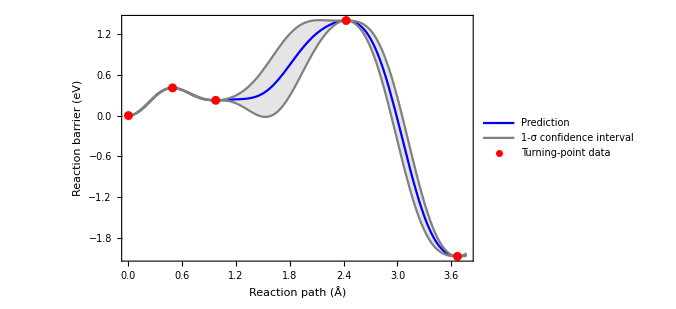

```mathematica
gp3a=With[{vol=3},Show[Plot[{Pdiste0sGradGP[[vol]][x],Pdiste0sGradGP[[vol]][x]+StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]],Pdiste0sGradGP[[vol]][x]-StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]]},{x,0,Evaluate[dist[[vol]][[-1]]+0.1]},PlotStyle->{Blue,Gray,Gray},Filling->{2->{3}},Exclusions->"None",PerformanceGoal->"Speed",PlotStyle->Thickness[
0.05],PlotLegends->Placed[{Style["Prediction",15],Style["1-σ confidence interval",15]},{0.25,0.2}],Frame->True,FrameTicksStyle->15,FrameLabel->{Style["Reaction path (Å)",FontSize->15],Style["Reaction barrier (eV)",FontSize->15]},ImageSize->500],ListPlot[diste0s[[vol]],PlotStyle->Red,PlotLegends->Placed[{Style["Turning-point data",15]},{0.20,0.35}]]]]
```

```mathematica
volshort=Table[vols[[i]][[1]],{i,1,3}]
list2=Partition[Flatten@Table[Join@Table[{volshort[[j]],i/10,Pdiste0sGradGP[[j]][i/10]},{i,-2,Floor[10*dist[[j]][[-1]]+3]}],{j,1,3}],3];
volDistE0GP={#1->#2&&#3}&@@@list2;
```

{4.6583,4.759,4.85}

```mathematica
ListPointPlot3D[list2,Filling->Bottom,FillingStyle->Directive[Thick],AxesLabel->{"Volume (Å^3)","Reaction Path (Å)","Reaction Barier \n(eV/defect)"}]
```

-Graphics3D-

```mathematica
Show[{ListPointPlot3D[list2,Filling->Bottom,FillingStyle->Directive[Thick],AxesLabel->{"Volume (Å^3)","Reaction Path (Å)","Energy \n(eV/defect)"},ImageSize->600],ListPlot3D[list2,Mesh->None,ColorFunction->"Rainbow",InterpolationOrder->3,PlotStyle->Opacity[0.15],BoundaryStyle->Directive[Black,Thick],Filling->Bottom,AxesLabel->{"Volume (Å^3)","Reaction Path (Å)","Energy \n(eV/defect)"}]}]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2}]
```

```mathematica
Show[{ListPointPlot3D[list2,FillingStyle->Directive[Thick],AxesLabel->{"Volume (Å^3)","Reaction Path (Å)","Reaction Barier \n(eV/defect)"},ImageSize->600],ListPlot3D[list2,Mesh->None,InterpolationOrder->3,PlotStyle->Directive[Opacity[0.8],Orange,Specularity[White,50]],BoundaryStyle->Directive[Black,Thick],Filling->Bottom,AxesLabel->{"Volume (Å^3)","Reaction Path (Å)","Reaction Barier \n(eV/defect)"}]}]
```

-Graphics3D-

```mathematica
FrameLabel->{Style["Reaction path (Å)",FontSize->12],Style["Reaction barrier (eV)",FontSize->12]}
```

```mathematica
neb0=Show[{ListPlot3D[list2,Mesh->None,InterpolationOrder->3,Axes->True,TicksStyle->15,PlotLabel->Style["Frenkel recombination energy surface",15],Filling->Bottom,Boxed->False,PlotStyle->Opacity[0.75],BoundaryStyle->Directive[Black,Thick],AxesLabel->{Style["Volume (Å)",FontSize->15],Style["Reaction Path (Å)",FontSize->15],Style["Reaction Barier \n(eV/defect)",FontSize->15]},ImageSize->400],ListPointPlot3D[list2,Filling->Bottom,FillingStyle->Directive[Thick]]}]
```

-Graphics3D-

```mathematica
neb1=Show[{ListPlot3D[list2,Mesh->None,InterpolationOrder->3,Axes->True,PlotLabel->"Frenkel recombination energy surface",Filling->Bottom,Boxed->False,PlotStyle->Opacity[0.75],BoundaryStyle->Directive[Black,Thick],AxesLabel->{Style["Volume (Å^3)",FontSize->12],Style["Reaction Path (Å)",FontSize->12],Style["Reaction Barier \n(eV/defect)",FontSize->12]},ImageSize->700],ListPointPlot3D[list2,Filling->Bottom,FillingStyle->Directive[Thick]]},ViewPoint->{3.9,3.5,2.8}]
```

-Graphics3D-

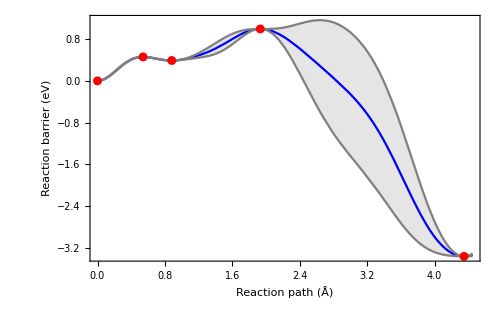

```mathematica
GraphicsGrid[{{gp1},{neb1}},ImageSize->700]
```

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/FRENKEL_RESULTS/Tall/Frenkel_Tall"];
fileFFE={"e0.out.m","e0_FS.out.m","VFE.Fqh_FS.out.m","VFE.Fqh_Fel_FS.out.m","VFE.Fqh_Fel.out.m","VFE.Fqh.out.m"};
FFEdata=Table[ReadList[fileFFE[[i]],{Number, Number}],{i,1,4}];
```

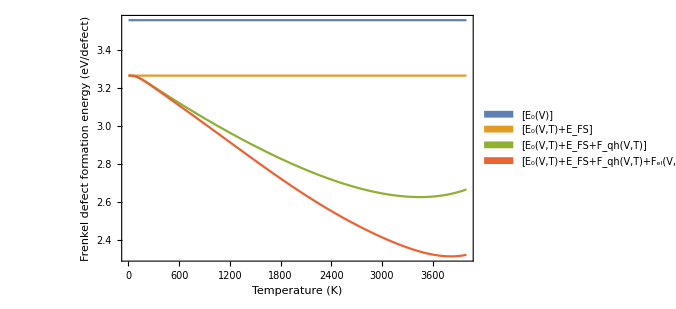

```mathematica
ListLinePlot[FFEdata,FrameLabel->{Style["Temperature (K)",12],Style["Frenkel defect formation energy (eV/defect)",12]},Frame->True,ImageSize->500,PlotLegends->Placed[SwatchLegend[{"[E_0(V)]","[E_0(V,T)+_E_FS]","[E_0(V,T)+E_FS+F_qh(V,T)]","[E_0(V,T)+E_FS+F_qh(V,T)+F_el(V,T)]"}],{0.77,0.54}]]
```

```mathematica
gibbs=Transpose[FFEdata[[4]]][[2]];
ttemp=Transpose[FFEdata[[4]]][[1]];
```

```mathematica
(*Gibbs and temperature lists*)
gibbs=Transpose[FFEdata[[4]]][[2]];
ttemp=Transpose[FFEdata[[4]]][[1]];
(*Multiplicity*)
m1=24;m2=16;m3=4;
```

```mathematica
(*Trimer is lowest energy defect at 3.622, trimer is next 4.010 then 4.628 *)
deltaDimer=3.622-4.010
deltaTrimerUnbound=3.622-4.628
deltaDimerUnbound=3.622-4.688
```

-0.388

-1.006

-1.066

```mathematica
(*Trimer concentration*)
tgibbsTrimer=Transpose@{ttemp,100*m1^0.5*Exp[-gibbs/(2*K2eV*ttemp)]};
(*Bound dimer*)
tgibbsDimer=Transpose@{ttemp,100*m1^0.5*Exp[-(gibbs-deltaDimer)/(2K2eV*ttemp)]};
(*Unbound trimer*)
tgibbsTrimerUnbound=Transpose@{ttemp,100*m2^0.5*Exp[-(gibbs-deltaTrimerUnbound)/(2K2eV*ttemp)]};
(*Unbound dimer*)
tgibbsDimerUnbound=Transpose@{ttemp,100*m3^0.5*Exp[-(gibbs-deltaDimerUnbound)/(2K2eV*ttemp)]};
(*Total*)
total=Transpose[{Transpose[tgibbsDimer][[1]],Transpose[tgibbsTrimer][[2]]+Transpose[tgibbsDimer][[2]]+Transpose[tgibbsTrimerUnbound][[2]]+Transpose[tgibbsDimerUnbound][[2]]}];
```

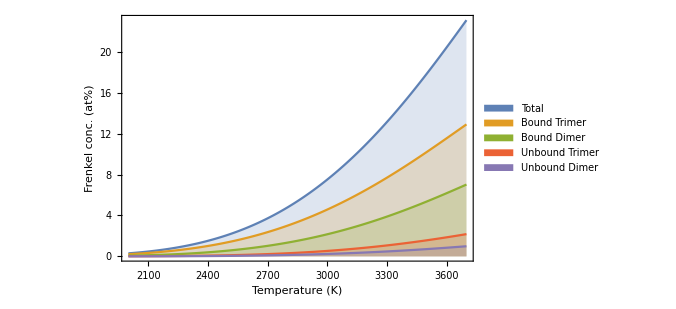

```mathematica
upper=3700;
lower=2000;
a=tgibbsTrimer[[lower;;upper]];
b=tgibbsDimer[[lower;;upper]];
c=tgibbsTrimerUnbound[[lower;;upper]];
d=tgibbsDimerUnbound[[lower;;upper]];
e=total[[lower;;upper]];

ListLinePlot[{e,a,b,c,d},Filling->Bottom,FrameLabel->{Style["Temperature (K)",12],Style["Frenkel conc. (at%)",12]},Frame->True,ImageSize->500,PlotLegends->Placed[SwatchLegend[{"Total","Bound Trimer","Bound Dimer","Unbound Trimer","Unbound Dimer"}],{0.15,0.5}],PlotRange->All]
```